```mathematica
Needs["MFGraphs`"]
```

```mathematica
Get["/Users/ribeirrd/Dropbox/My Mac (kl-14835.kaust.edu.sa)/Documents/workspace/MFGraphs/MFGraphs/MFGraphs.m"](*Ricardo, use this when not running from eclipse.*)
```

```mathematica
Names["MFGraphs`*"]
```

{A,alpha,AtHead,AtTail,A$,beta,DataG,DataToEquations,EqEliminatorX,F,FixedPointSolverStepX,FixedSolverStepX2,g,g$2733,H,I1,I2,Intg,m,m$,n,OtherWay,p,Parameters,p$,S1,S10,S11,S12,S13,S14,S15,S16,S2,S3,S4,S5,S6,S7,S8,S9,StartSolverX,Test,TransitionsAt,triple2path,U1,U2,V,V$2733,W,W$2733,x,x$}

### Using the new functions in IterationFunction.m

```mathematica
Data=DataG[25];
MFGEquations=DataToEquations[Data];
```

DataToEquations: Finished assembling strucural equations:

DataToEquations: Critical case ...

DataToEquations: Reducing ...

EqEliminatorX: Reached a solution!

DataToEquations: Done.

```mathematica
Keys[MFGEquations]
```

{FG,EqAllAll,reduced,Nlhs,EqCriticalCase,criticalreduced,Nrhs,EqGeneralCase}

```mathematica
MFGEquations["EqGeneralCase"]/.MFGEquations["criticalreduced"][[2]]
```

-3+j481+u496==-0.324624&&-5+j481+u498==0.

```mathematica
<|x->4, v->x|>/.{x->3}
```

<|x→4,v→3|>

#### Non-linear case

```mathematica
MFGEquations["EqGeneralCase"]
```

-j481-u496+u501==-j481+Intg[-j481]&&2-j481-u498+u503==2-j481+Intg[2-j481]

```mathematica
KeySort[MFGEquations["criticalreduced"][[2]]]//Simplify
```

<|j575→0,j576→2,j577→2-2,j578→2-2,j579→2,j580→2,j581→0,j582→0,j583→0,j584→0,jt585→2,jt586→0,jt587→0,jt588→0,jt589→0,jt590→0,jt591→2,jt592→2-2,jt593→2-2,jt594→0,u595→1,u596→1,u597→3,u598→5,u599→3,u600→2+1,u601→1,u602→-2+2+3,u603→5,u604→3|>

```mathematica
MFGEquations["criticalreduced"][[2]]/.MFGEquations["criticalreduced"][[2]]
```

<|j579→2,u601→1,u603→5,j575→0,j576→2,j577→2-2,j578→2-2,j581→0,j582→0,j583→0,j584→0,jt585→2,jt586→0,jt587→0,jt588→0,jt589→0,jt590→0,jt591→2,jt592→2-2,jt593→2-2,jt594→0,u596→1,u598→5,u604→3,u600→2+1,u602→-2+2+3,j580→2,u595→1,u597→3,u599→3|>

```mathematica
FixedSolverStepX2[MFGEquations][MFGEquations["criticalreduced"][[2]]
]
```

Step: Reducing ...

EqEliminatorX: Reached a solution!

<|j579→2,u601→1,u603→5,j575→0,j576→2.,j577→2-2.,j578→2-2.,j581→0,j582→0,j583→0,j584→0,jt585→2.,jt586→0,jt587→0,jt588→0,jt589→0,jt590→0,jt591→2.,jt592→2-2.,jt593→2-2.,jt594→0,u596→1,u598→5,u604→2.67538,u600→-0.324624+1. 2.+1. 1.,u602→-2.+1. 2.+1. 2.67538,j580→2.,u595→1.,u597→2.67538,u599→2.67538|>

```mathematica
MFGEquations["EqGeneralCase"]/.%
```

True

```mathematica
FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced"][[2]],10]
```

Step: Reducing ...

EqEliminatorX: Reached a solution!

Step: Reducing ...

EqEliminatorX: Reached a solution!

<|j579→2,u601→1,u603→5,j575→0,j576→2.,j577→2-2.,j578→2-2.,j581→0,j582→0,j583→0,j584→0,jt585→2.,jt586→0,jt587→0,jt588→0,jt589→0,jt590→0,jt591→2.,jt592→2-2.,jt593→2-2.,jt594→0,u596→1,u598→5,u604→2.67538,u600→-0.324624+1. 2.+1. 1.,u602→-2.+1. 2.+1. 2.67538,j580→2.,u595→1.,u597→2.67538,u599→2.67538|>

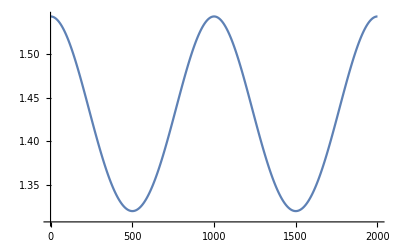

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.